## Load data so we can get tid string

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Options

```mathematica
fName="20180817-orb_1607-densPA_45-sRate0_63-Mathematica.csv";
```

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
Options[loadJVCSV]={printFName->False};
loadJVCSV[OptionsPattern[]]:=Module[{},
If[OptionValue[printFName],Print[fName]];(*
data=Cases[Import[inDir<>fName,"Table"],{_?NumberQ,___}];
data=Cases[Import[inDir<>fName,"Table"],{_?StringQ,___}]*)
data=Import[inDir<>fName,{"CSV","Data"},"HeaderLines"-> 1]
]
```

Header line

```mathematica
Import[inDir<>fName,{"Data",1,All}]//TableForm[#,TableDirections->Row]&
```

Tid | pot | potErr | cur | curErr | je | jeerr | nDown | nDownErr | downEpot | downEpotErr

Load variables

```mathematica
data=loadJVCSV[];
```

```mathematica
{tids,pots,potErrs,curs,curErrs,jes,jeErrs,dens,densErrs,densPots,densPotErrs}=data[[All,#]]&/@Range[1,11];
```

### Select times/indices

```mathematica
interval=2;
```

```mathematica
itvlTidStr=Switch[interval,
1,
{{"12:00:28.5","12:00:38.7"},{"12:00:40.0","12:00:48"}},
2,
{"01:04:28.5","01:04:41"} ;
Switch[fName,
"20180817-orb_1607-densPA_45-sRate0_63-Mathematica.csv",
{"01:04:29.3","01:04:40.5"},
"20180817-orb_1607-densPA_45-sRate1_89-Mathematica.csv",
{"01:04:29.3","01:04:41.5"},
"20180817-orb_1607-densPA_45-sRate0_31-Mathematica.csv",
{"01:04:29.3","01:04:41.5"}]
];
```

```mathematica
itvlBounds=Switch[Length@Dimensions[itvlTidStr],
1,
Flatten@((minTidInd[#,tids])&/@itvlTidStr),
2,

{Flatten@((minTidInd[#,tids])&/@itvlTidStr[[1,;;]]),Flatten@((minTidInd[#,tids])&/@itvlTidStr[[2,;;]])}
];
```

```mathematica
tids[[#]]&/@itvlBounds
```

{01:04:28.695,01:04:40.055}

```mathematica
inds1=Switch[Length@Dimensions[itvlTidStr],
1,
Range@@itvlBounds,
2,
Flatten[{Range@@itvlBounds[[1,;;]],Range@@itvlBounds[[2,;;]]}]
];
```

```mathematica
tid=tids[[inds1]];
```

## Load other things

```mathematica
nTrials=1000;
```

```mathematica
SetDirectory["/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180815/"]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180815

```mathematica
kFiles=FileNames[RegularExpression["Orb1607_itvl2_kappa-fixT90eV.*nVJVJeV(-\\d\\d)?.wdx"]]
```

{Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV-01.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV-02.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV-03.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-01.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-02.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-03.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-04.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-05.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-06.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-07.wdx,Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV.wdx}

If you want the version showing what we got from simulations with fixT=90 eV for the Maxwellian fits, check THIS out

```mathematica
checkout90eVMaxwellianFiles=False;
```

```mathematica
gFiles=If[checkout90eVMaxwellianFiles,{"Orb1607_itvl2_Maxwell-fixT90eV_nRolls1000_nVJVJeV.wdx"},FileNames[RegularExpression["Orb1607_itvl2_Maxwell-fixT70eV.*nVJVJeV(-\\d\\d)?.wdx"]]]
```

{Orb1607_itvl2_Maxwell-fixT70eV_nRolls1000_nVJVJeV.wdx,Orb1607_itvl2_Maxwell-fixT70eV_nRolls1100_nVJVJeV.wdx}

RESTORE DATA FILES

```mathematica
For[i=1,i≤ Length@kFiles,i++,
Print[kFiles[[i]]];
If[FileExistsQ[kFiles[[i]]],
Print[Ja];
<<(kFiles[[i]]);
If[i==1,
kMCValsMaster=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
kMCValsMaster = Transpose[(Transpose[kMCValsMaster]~Join~Transpose[kMCVals])];
];
];
]
```

Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV-01.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV-02.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV-03.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls125_nVJVJeV.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-01.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-02.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-03.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-04.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-05.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-06.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV-07.wdx

Ja

Orb1607_itvl2_kappa-fixT90eV_nRolls200_nVJVJeV.wdx

Ja

```mathematica
For[i=1,i≤ Length@gFiles,i++,
Print[gFiles[[i]]];
If[FileExistsQ[gFiles[[i]]],
Print[Ja];
<<(gFiles[[i]]);
If[i==1,
gMCValsMaster=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
gMCValsMaster = Transpose[(Transpose[gMCValsMaster]~Join~Transpose[gMCVals])];
];
];
]
```

Orb1607_itvl2_Maxwell-fixT70eV_nRolls1000_nVJVJeV.wdx

Ja

Orb1607_itvl2_Maxwell-fixT70eV_nRolls1100_nVJVJeV.wdx

Ja

```mathematica
kMCValsMaster//Dimensions
```

{4,2100}

```mathematica
gMCValsMaster//Dimensions
```

{4,2100}

```mathematica
kMCValsSub = kMCValsMaster[[;;,1;;2000]];
```

```mathematica
kMCValsSub//Dimensions
```

{4,2000}

```mathematica
gMCValsSub = gMCValsMaster[[;;,1;;2000]];
```

```mathematica
gMCValsSub//Dimensions
```

{4,2000}

```mathematica
nTrialsK=(kMCValsSub//Dimensions)[[2]];
nTrialsG=(gMCValsSub//Dimensions)[[2]];
```

```mathematica
kMCVals=kMCValsSub;
gMCVals=gMCValsSub;
Clear[kMCValsMaster,gMCValsMaster,kMCValsSub,gMCValsSub];
```

## Plots!

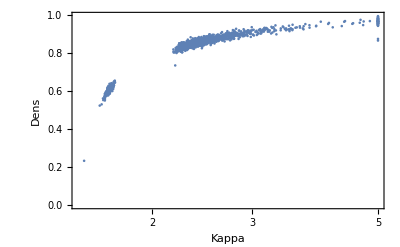

```mathematica
ListLogLinearPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[1,;;]]],2],Frame->True,FrameLabel->{"Kappa","Dens"}]
```

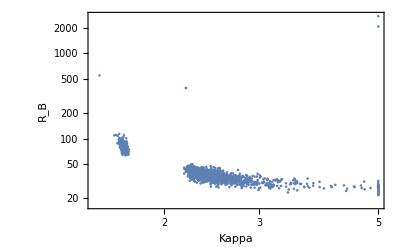

```mathematica
ListLogLogPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[3,;;]]],2],Frame->True,FrameLabel->{"Kappa","R_B"}]
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","Log_10R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{100},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:={{1.25,2.1},{0.52,1.05}};
```

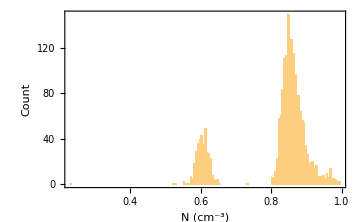
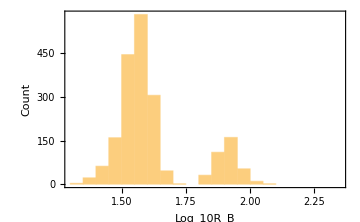
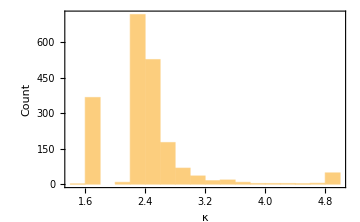
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[If[MCParmInd==3,Log10[kMCVals[[MCParmInd]]],kMCVals[[MCParmInd]]],If[MCParmInd==3,Automatic,binSizes[[MCParmInd]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

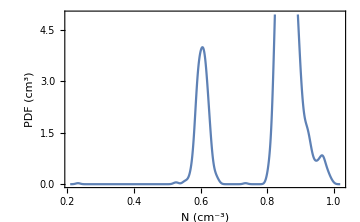
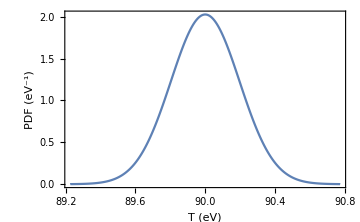
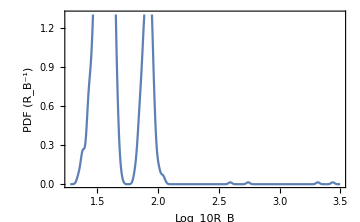
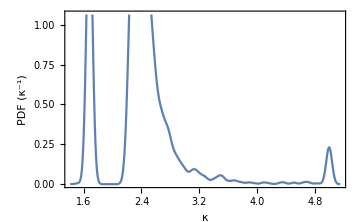

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

## Nye vei, med RE axis

```mathematica
axVals={{3.16,1.53}, {10,2.19}, {31.6,3.17}, {100,4.56}, {316,6.55}, {1000,9.66}, {3162,14.26}, {10000,15.66}, {20000,15.67}};
```

```mathematica
xVals=Round[Log10[axVals[[;;,1]]]*10]/10.//N;
```

```mathematica
log10XwithY=Partition[Riffle[xVals,axVals[[;;,2]]],2];
```

```mathematica
this=Interpolation[log10XwithY]
```

InterpolatingFunction[…]

```mathematica
RBVals={1.4,1.6,1.8,2.0};
```

```mathematica
REVals=this[RBVals]
```

{2.94408,3.40912,3.94264,4.56}

```mathematica
REValsRound=Round[REVals*10]/10.
```

{2.9,3.4,3.9,4.6}

```mathematica
tics=Line[{{#,0.4+0.005},{#,0.4-0.005}}&/@RBVals]
```

Line[{{{1.4,0.405},{1.4,0.395}},{{1.6,0.405},{1.6,0.395}},{{1.8,0.405},{1.8,0.395}},{{2.,0.405},{2.,0.395}}}]

```mathematica
text=Text[#[[2]],{#[[1]],0.35}]&/@Partition[Riffle[RBVals,REValsRound],2]
```

{Text[2.9,{1.4,0.35}],Text[3.4,{1.6,0.35}],Text[3.9,{1.8,0.35}],Text[4.6,{2.,0.35}]}

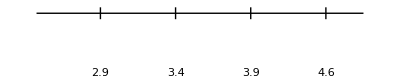

```mathematica
axis=Graphics[{Line[{{1.23,0.4},{2.1,0.4}}],tics,text}]
```

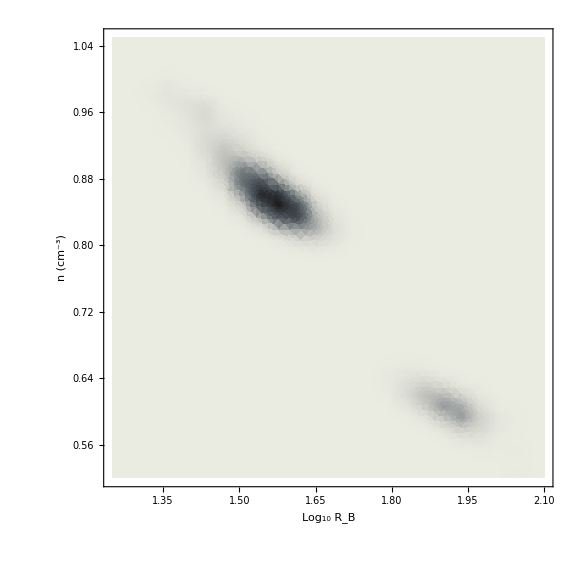

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotRangeClipping->False]
```

Maxwellian plots

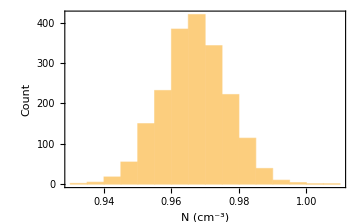
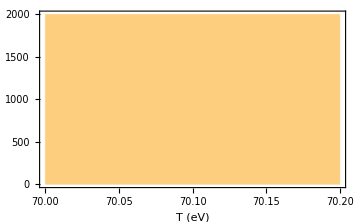
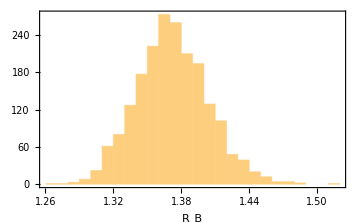

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

```mathematica
mWellTitle=If[checkout90eVMaxwellianFiles,ToString@StringForm["`1` (Mwell, N=`2`, fixT=`3`eV)",MCTitle,nTrialsG,90],ToString@StringForm["`1` (Maxwell, N = `2`)",MCTitle,nTrialsG]];
```

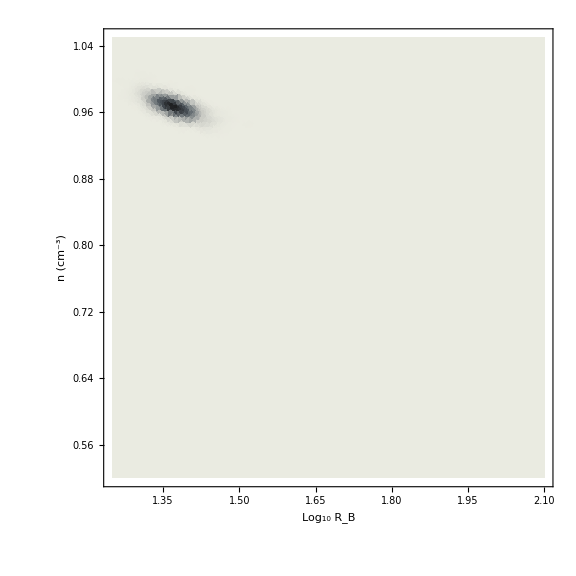

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[mWellTitle,Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

## Gammel vei, uten RE axis

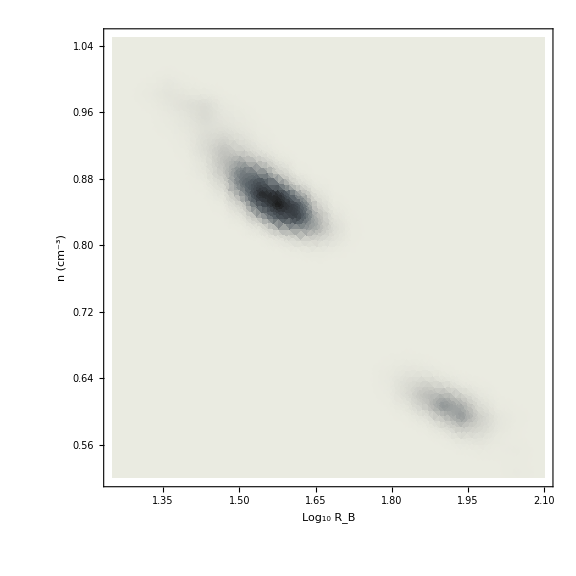

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

Maxwellian plots

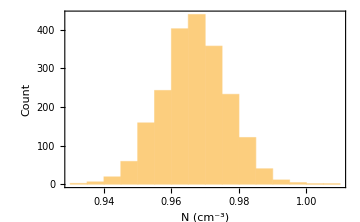
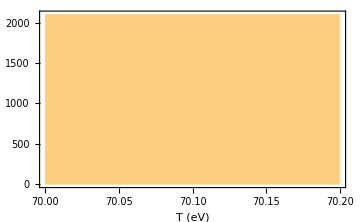
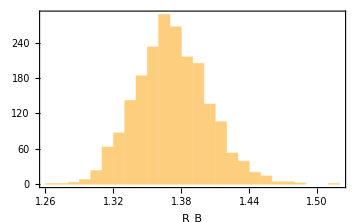

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

```mathematica
mWellTitle=If[checkout90eVMaxwellianFiles,ToString@StringForm["`1` (Mwell, N=`2`, fixT=`3`eV)",MCTitle,nTrialsG,90],ToString@StringForm["`1` (Maxwell, N = `2`)",MCTitle,nTrialsG]];
```

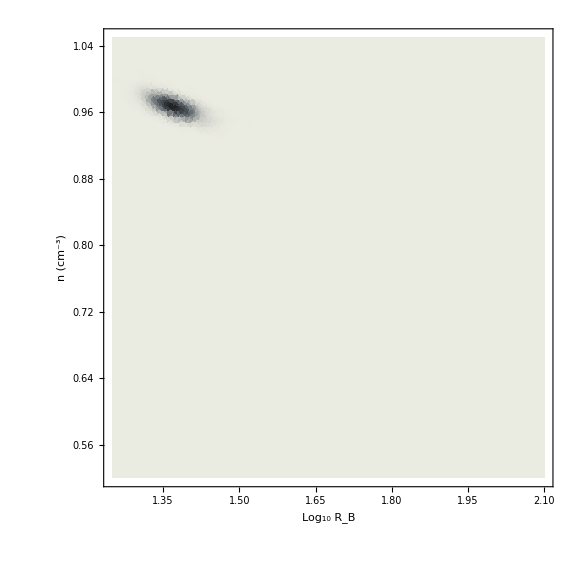

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[mWellTitle,Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```